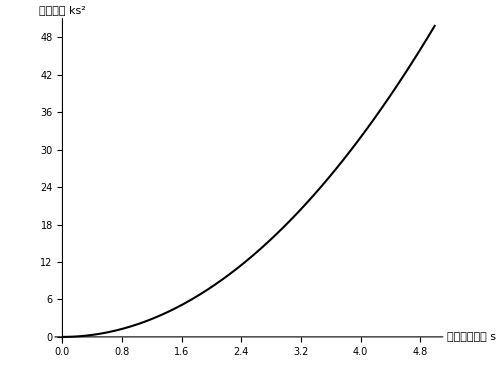

```mathematica
plot=Plot[2 x^2,{x,0,5},
PlotStyle->{Black,AbsoluteThickness[1.5]},(*曲线粗细和颜色*)
AxesStyle->Directive[FontFamily->"Times New Roman",FontSize->15,Black,AbsoluteThickness[1.5]],(*坐标轴粗细*)
TicksStyle->Directive[Black,FontFamily->"Times New Roman"],(*刻度标签样式*)
AspectRatio->3/4,(*图像宽高比*)
ImageSize->500,(*图像大小*)
AxesLabel->{"物流服务水平 s","物流成本 ks^2"},(*坐标轴标签*)
LabelStyle->{FontFamily->"Times New Roman",FontSize->12,Black},(*全局文本样式*)BaseStyle->{FontFamily->"Times New Roman"},(*确保所有文本继承此字体*)PlotRange->All                     (*显示所有数据*)]
```

```mathematica
Export["D:/my blogs/source/_posts/从模型构建到求解分析：Mathematica在OM研究中的应用/plot.png",plot,ImageResolution->300]
```

D:/my blogs/source/_posts/从模型构建到求解分析：Mathematica在OM研究中的应用/plot.png

```mathematica
(*明确约束条件*)
```

```mathematica
$Assumptions=θ>0&&β>0&&k>0&&4k-β^2>0&&0<α<1;
```

```mathematica
(*为四个情景下的均衡物流水平s赋值*)
```

```mathematica
sRS=(β θ)/(8k-β^2);sRP=(β θ)/(2(4k-β^2));sMS=((1-α)β θ)/(4k-(1-α)β^2);sMP=(β θ)/(4k(2-α)-β^2);
```

```mathematica
(*Proposition 1(a)，比较RS和RP情景下的均衡s*)
```

```mathematica
(*类似这种简单的表达式，Reduce函数可以迅速判断其大小关系;遇到复杂函数时建议不要依赖Reduce，尽量从函数单调性入手去分析*)
```

```mathematica
Reduce[$Assumptions&&sRP-sRS>0]
Reduce[$Assumptions&&sRP-sRS<0]
```

0<α<1&&β>0&&k>β^2/4&&θ>0

False

```mathematica
(*将表达式稍微变形，结合约束条件也不难判断函数大小关系*)
```

```mathematica
Simplify[sRP-sRS]
```

(β^3 θ)/(64 k^2-24 k β^2+2 β^4)

```mathematica
Factor[64 k^2-24 k β^2+2 β^4]
```

2 (4 k-β^2) (8 k-β^2)

```mathematica
sRP-sRS=(β^3 θ)/(64 k^2-24 k β^2+2 β^4)=(β^3 θ)/(2 (4 k-β^2) (8 k-β^2))>0
```

```mathematica
(*Proposition 1(b)，比较MS和MP情景下的均衡s*)
```

```mathematica
(*佣金率α的基础范围是(0,1)，然而论文在脚注中提到α<α^*这个约束条件，但未出给具体表达式，因此我们实际上是在一个更宽松的约束范围内比较函数大小，所以结果与论文有所出入*)
```

```mathematica
Reduce[$Assumptions&&sMP-sMS>0]
Reduce[$Assumptions&&sMP-sMS<0]
```

β>0&&1/2 (3-√5)<α<1&&k>β^2/4&&θ>0

β>0&&0<α<1/2 (3-√5)&&k>β^2/4&&θ>0

```mathematica
Simplify[sMS-sMP]
```

-(4 k (1-3 α+α^2) β θ)/((4 k (-2+α)+β^2) (4 k+(-1+α) β^2))

```mathematica
Factor[-((4 k (-2+α)+β^2) (4 k+(-1+α) β^2))]
```

-(-8 k+4 k α+β^2) (4 k-β^2+α β^2)

```mathematica
(*根据约束条件和Proposition 1(b) sMS-sMP>0的结果来看，至少在α∈(0, α^*)范围内1-3 α+α^2>0是成立的，因此后续分析我们以1-3 α+α^2>0近似地替代约束条件α<α^**)
```

```mathematica
sMS-sMP=-(4 k (1-3 α+α^2) β θ)/((4 k (-2+α)+β^2) (4 k+(-1+α) β^2))=(4 k  β θ(1-3 α+α^2))/((4k-β^2+4k-4 k α) (4 k-β^2+α β^2)>0)
```

```mathematica
(*Proposition 1(c)，比较MS和MP情景下的均衡s*)
```

```mathematica
(*由(a)(b)可知，sRP>sRS和sMS>sMP，因此综合比较四个情景实际上也只是比较sRP和sMS*)
```

```mathematica
(*根据Reduce结果可知sRP-sMS>0和sRP-sMS<0两种结果均存在，但这个结果显然不够简洁*)
```

```mathematica
Reduce[$Assumptions&&1-3 α+α^2>0&&sRP-sMS>0]
Reduce[$Assumptions&&1-3 α+α^2>0&&sRP-sMS<0]
```

β>0&&0<α<1/2 (3-√5)&&β^2/4<k<(-β^2+α β^2)/(-4+8 α)&&θ>0

β>0&&0<α<1/2 (3-√5)&&k>(-β^2+α β^2)/(-4+8 α)&&θ>0

```mathematica
(*化简表达式，我们会发现一些相乘的项实际上恒大于0的，这意味着我们在分析中可以将其剥离，因为它们并不影响函数符号的正负，即我们仅需分析(-4 k+8 k α+β^2-α β^2)即可判断函数大小关系*)
```

```mathematica
Together[sRP-sMS]
```

(β (4 k-8 k α-β^2+α β^2) θ)/(2 (-4 k+β^2) (4 k-β^2+α β^2))

```mathematica
sRP-sMS=(β (4 k-8 k α-β^2+α β^2) θ)/(2 (-4 k+β^2) (4 k-β^2+α β^2))=(β  θ)/(2 (4 k-β^2) (4 k-β^2+α β^2))(-4 k+8 k α+β^2-α β^2)
```

```mathematica
(*原文令τ=β^2/k，此处我们与原文保持一致*)
```

```mathematica
-4 k+8 k α+β^2-α β^2=-4 +8  α+τ-α τ
```

```mathematica
(*τ系数是1-α，说明关于τ单调递增，令该式子=0即可求得阈值;
若τ>(-4+8 α)/(-1+α)，sRP>max{sRS,sMS,sMP}，若τ≤(-4+8 α)/(-1+α)，sMS≥max{sRP,sRS,sMP}*)
```

```mathematica
Collect[(-4 +8  α+τ-α τ),τ]
```

-4+8 α+(1-α) τ

```mathematica
Simplify[Solve[-4+8 α+(1-α) τ==0,τ]]
```

{{τ→(-4+8 α)/(-1+α)}}